# Feature extractor with images ranged between 0.2 to 3 Miles

## Neural net initilization

```mathematica
ClearAll["Global`*"]
```

```mathematica
ClearAll[tnet]
tnet = Import[File["/Users/mehmetsahin/Downloads/2017-12-27T18-42-44_0_0123_05898_3.71e-3_9.47e-2.wlnet"]]
```

NetChain[<>]

```mathematica
choppedTNet = NetTake[tnet,1]
```

NetChain[<>]

## Functions

```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
ClearAll[fromFileNameGetGeoRange,fileLocation]

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];

fileLocation[folderName_, hash_] := 
	FileNameJoin[{NotebookDirectory[],"features",folderName,IntegerString[Hash[hash], 36]<>".wxf"}]
```

```mathematica
getFileNames["validation"]//Length
```

```mathematica
ClearAll[getFileNames]
getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

getwxfFileNames[folderName_] := 
	FileNames["*.wxf",FileNameJoin[{NotebookDirectory[],"features",folderName}],Infinity];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_List] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		fileNames
	]
```

```mathematica
binaryWrite[expr_]:=binaryWrite[expr,CreateFile[]];
binaryWrite[expr_,file_]:=With[{bytes=BinaryWrite[file,BinarySerialize[expr]]},Close[file];
bytes];
binaryRead[file_]:=BinaryDeserialize[ReadByteArray[file]];
```

```mathematica
getFileNames["training"][[1]]
```

/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/training/ODpBAy1TBVBvaW50ZgJzBExpc3Ry01C6eRvvPUBym~t0Ps7ZV8AtUwRab29tcgbEcAYDiMQ~LVMIR2VvUmFuZ2VyiFZ9gdBZ~D8=/ODpBAi1TCEdlb1JhbmdlcohWfYHQWew~LVMGTnVtYmVyQwE=.png

```mathematica
fileLocation["training","asda"]
```

/Users/mehmetsahin/Desktop/GitHubWL/Summer2018Starter/Project/CitiyImages0.2-10/features/training/1n7spk599ajwb.wxf

```mathematica
ClearAll[storeTheFeatures]

storeTheFeatures[folderName_String,batchSize_:1000] := 
	storeTheFeatures[folderName, associateFilesToGeoRange[getFileNames[folderName]],batchSize]

storeTheFeatures[folderName_String, dataFiles_List, batchSize_] := 
	DynamicModule[
		{filename, print = "Starting job"},
		PrintTemporary[Dynamic[print]];
		MapIndexed[
			Function[
				{partitionedDataFiles, index},
				filename = fileLocation[folderName, Keys[partitionedDataFiles]];
				If[
					Not @ FileExistsQ @ filename,
					binaryWrite[
						Thread[
							choppedTNet[Keys[partitionedDataFiles]] -> Values[partitionedDataFiles]
						], 
						filename
					];
					print = StringJoin[{"Part ", index, " of ", Length[dataFiles] / batchSize, " is Done"}    /. s:Except[_String] :> ToString[s]]
				]
			],
			Partition[dataFiles, batchSize]
		]	
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

### Export the data:

validation features:

```mathematica
storeTheFeatures["validation",350];
```

training features:

```mathematica
storeTheFeatures["training",1149];
```

testing features:

```mathematica
storeTheFeatures["testing",350];
```

### Import the data:

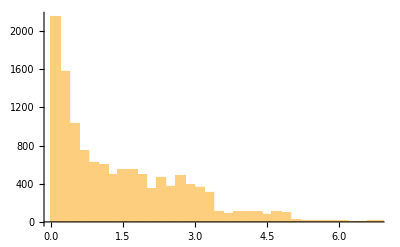

```mathematica
associateFilesToGeoRange[getFileNames["training"]][[All,2]]//Histogram
```

```mathematica
trainFeatures = RandomSample @ Flatten @ Join[Map[binaryRead,getwxfFileNames["training"]]];
validationFeatures = RandomSample @ Flatten @ Join[Map[binaryRead,getwxfFileNames["validation"]]];
testFeatures = RandomSample @ Flatten @ Join[Map[binaryRead,getwxfFileNames["testing"]]];
```

```mathematica
trainFeatures//Length
testFeatures//Length
```

12639

1050

## Import data from 0 to 3: Done

```mathematica
validationFeaturesSmall = TakeSmallestBy[validationFeatures,Last,UpTo[1810]];
trainFeaturesSmall = TakeSmallestBy[trainFeatures,Last,UpTo[10850]];
testFeaturesSmall = TakeSmallestBy[testFeatures,Last,UpTo[900]];
validationFeaturesSmall[[All,2]]//MinMax
trainFeaturesSmall[[All,2]]//MinMax
testFeaturesSmall[[All,2]]//MinMax
```

{0.0666667,2.99197}

{0.0666667,2.98346}

{0.0666667,2.98972}

```mathematica
validationFeaturesSmallRandom = RandomSample[validationFeaturesSmall];
trainFeaturesSmallRandom = RandomSample[trainFeaturesSmall];
testFeaturesSmallRandom = RandomSample[testFeaturesSmall];
```

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{ConvolutionLayer[32,2,"Stride"->2,"Input"->{512,8,8}],Ramp,FlattenLayer[],LinearLayer[100],Ramp,LinearLayer[1],Abs},"Input"->{512,8,8},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeaturesSmallRandom,ValidationSet->validationFeaturesSmallRandom]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test;

```mathematica
calculateError[trainedTnet3,testFeaturesSmallRandom]
```

0.790807

## Import data from 0 to 2: Done

```mathematica
ClearAll[validationFeaturesSmall,trainFeaturesSmall,testFeaturesSmall]
validationFeaturesSmall = TakeSmallestBy[validationFeatures,Last,UpTo[1470]];
trainFeaturesSmall = TakeSmallestBy[trainFeatures,Last,UpTo[8800]];
testFeaturesSmall = TakeSmallestBy[testFeatures,Last,UpTo[730]];
validationFeaturesSmall[[All,2]]//MinMax
trainFeaturesSmall[[All,2]]//MinMax
testFeaturesSmall[[All,2]]//MinMax
```

{0.0666667,1.9789}

{0.0666667,1.98946}

{0.0666667,1.99343}

```mathematica
ClearAll[validationFeaturesSmallRandom,trainFeaturesSmallRandom,testFeaturesSmallRandom]
validationFeaturesSmallRandom = RandomSample[validationFeaturesSmall];
trainFeaturesSmallRandom = RandomSample[trainFeaturesSmall];
testFeaturesSmallRandom = RandomSample[testFeaturesSmall];
```

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{ConvolutionLayer[64,2,"Stride"->2,"Input"->{512,8,8}],Ramp,FlattenLayer[],LinearLayer[512],Ramp,LinearLayer[1],Abs},"Input"->{512,8,8},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeaturesSmallRandom,ValidationSet->validationFeaturesSmallRandom]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test;

```mathematica
calculateError[trainedTnet3,testFeaturesSmallRandom]
```

0.606948

## Import data from 0 to 1: Done

```mathematica
ClearAll[validationFeaturesSmall,trainFeaturesSmall,testFeaturesSmall]
validationFeaturesSmall = TakeSmallestBy[validationFeatures,Last,UpTo[1010]];
trainFeaturesSmall = TakeSmallestBy[trainFeatures,Last,UpTo[6100]];
testFeaturesSmall = TakeSmallestBy[testFeatures,Last,UpTo[510]];
validationFeaturesSmall[[All,2]]//MinMax
trainFeaturesSmall[[All,2]]//MinMax
testFeaturesSmall[[All,2]]//MinMax
```

{0.0666667,0.978668}

{0.0666667,0.991014}

{0.0666667,0.989226}

```mathematica
ClearAll[validationFeaturesSmallRandom,trainFeaturesSmallRandom,testFeaturesSmallRandom]
validationFeaturesSmallRandom = RandomSample[validationFeaturesSmall];
trainFeaturesSmallRandom = RandomSample[trainFeaturesSmall];
testFeaturesSmallRandom = RandomSample[testFeaturesSmall];
```

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{ConvolutionLayer[64,2,"Stride"->2,"Input"->{512,8,8}],Ramp,FlattenLayer[],LinearLayer[512],Ramp,LinearLayer[1],Abs},"Input"->{512,8,8},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeaturesSmallRandom,ValidationSet->validationFeaturesSmallRandom]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test;

```mathematica
calculateError[trainedTnet3,testFeaturesSmallRandom]
```

0.513625

## Import data from 0 to 1: Done

```mathematica
ClearAll[validationFeaturesSmall,trainFeaturesSmall,testFeaturesSmall]
validationFeaturesSmall = TakeSmallestBy[validationFeatures,Last,UpTo[590]];
trainFeaturesSmall = TakeSmallestBy[trainFeatures,Last,UpTo[3595]];
testFeaturesSmall = TakeSmallestBy[testFeatures,Last,UpTo[303]];
validationFeaturesSmall[[All,2]]//MinMax
trainFeaturesSmall[[All,2]]//MinMax
testFeaturesSmall[[All,2]]//MinMax
```

{0.0666667,0.386041}

{0.0666667,0.38138}

{0.0666667,0.38992}

```mathematica
ClearAll[validationFeaturesSmallRandom,trainFeaturesSmallRandom,testFeaturesSmallRandom]
validationFeaturesSmallRandom = RandomSample[validationFeaturesSmall];
trainFeaturesSmallRandom = RandomSample[trainFeaturesSmall];
testFeaturesSmallRandom = RandomSample[testFeaturesSmall];
```

```mathematica
ClearAll[finalLayers]
finalLayers =NetChain[{ConvolutionLayer[64,2,"Stride"->2,"Input"->{512,8,8}],Ramp,FlattenLayer[],LinearLayer[512],Ramp,LinearLayer[1],Abs},"Input"->{512,8,8},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
ClearAll[trainedTnet3]
trainedTnet3 = NetTrain[finalLayers,trainFeaturesSmallRandom,ValidationSet->validationFeaturesSmallRandom]
```

NetChain[<>]

```mathematica
ClearAll[newTrainedNet]
newTrainedNet = NetJoin[choppedTNet,trainedTnet3]
```

NetChain[<>]

### Test;

```mathematica
calculateError[trainedTnet3,testFeaturesSmallRandom]
```

0.490418